Here we made the main graphs of FF,CV2, and mean of un-regulated, auto-regulated, activator-inhibitor, simple activation and inhibition gene systems. These were estimated using the GA (FRM) algorithm

### Setting directory

```mathematica
SetDirectory["/media/lina/DATA/SimulacionesTesis/resultadosS4/csv"];
```

## Graphs for each regulatory system

### Importing data

```mathematica
(*******************************)
```

```mathematica
(**********************************)
```

```mathematica
data=ToExpression@Table[Import["controlUnRGA_γg"<>i<>".csv"],{i,{"0.5","1.","1.5","2"}}];
```

```mathematica
data=ToExpression@ImportString[#,"CSV"]&/@Table[Import["controlRGA_γg"<>i<>"2"],{i,{"0.5","1.","1.5.","2."}}];
```

```mathematica
data=ToExpression@ImportString[#,"CSV"]&/@Table[Import["controlAIGAA_Aγg"<>i],{i,{"0.5","1.","1.5","2"}}];
```

```mathematica
data=ToExpression@ImportString[#,"CSV"]&/@Table[Import["controlAIGAA_Iγg"<>i],{i,{"0.5","1.","1.5","2"}}];
```

```mathematica
data=ToExpression@ImportString[#,"CSV"]&/@Table[Import["controlAIGAI_Aγg"<>i],{i,{"0.5","1.","1.5","2"}}];
```

```mathematica
data=ToExpression@ImportString[#,"CSV"]&/@Table[Import["controlAIGAI_Iγg"<>i],{i,{"0.5","1.","1.5","2"}}];
```

```mathematica
data=ToExpression@ImportString[#,"CSV"]&/@Table[Import["controlABGAA_AAγg"<>i],{i,{"0.5","1.","1.5","2"}}];
```

```mathematica
data=ToExpression@ImportString[#,"CSV"]&/@Table[Import["controlABGAA_IAγg"<>i],{i,{"0.5","1.","1.5","2"}}];
```

```mathematica
data=ToExpression@ImportString[#,"CSV"]&/@Table[Import["controlABGAA_AI2γg"<>i],{i,{"0.5","1.","1.5","2"}}];
```

```mathematica
data=ToExpression@ImportString[#,"CSV"]&/@Table[Import["controlABGAA_II2γg"<>i],{i,{"0.5","1.","1.5","2"}}];
```

```mathematica
data=ToExpression@ImportString[#,"CSV"]&/@Table[Import["controlABGAI_AIγg"<>i],{i,{"0.5","1.","1.5","2"}}];
```

```mathematica
data=ToExpression@ImportString[#,"CSV"]&/@Table[Import["controlABGAI_IIγg"<>i],{i,{"0.5","1.","1.5","2"}}];
```

```mathematica
data=ToExpression@ImportString[#,"CSV"]&/@Table[Import["controlABGAI_AAγg"<>i],{i,{"0.5","1.","1.5","2"}}];
```

```mathematica
data=ToExpression@ImportString[#,"CSV"]&/@Table[Import["controlABGAI_IAγg"<>i],{i,{"0.5","1.","1.5","2"}}];
```

```mathematica
(******************************************+)
```

```mathematica
data=ToExpression@ImportString[#,"CSV"]&/@data;
```

ImportString::string: First argument {{5.130868339632227, 0.030576301288972742, 6819752100336479882/39317994149906175}","{5.988978492855897, 0.05860090138233402, 62027909245983505318196982261067762924160147/530996012619119368169709446383932141621600}","{3.6094182116218634, 0.04312378568089…{3.817439046929542, 0.2309887856766875, 5025735753624129678756081275833827222470803/290386494963161874977645119639861390075200}","{4.635051991517199, 0.29292668512955145, 15813878361998859462541801093223888277809/971756210846650734559489307039180496000}} is not a string.

ToExpression::notstrbox: ImportString[{{5.130868339632227, 0.030576301288972742, 6819752100336479882/39317994149906175}","{5.988978492855897, 0.05860090138233402, 62027909245983505318196982261067762924160147/530996012619119368169709446383932141621600}","{3.6094182116218634, 0.043123…046929542, 0.2309887856766875, 5025735753624129678756081275833827222470803/290386494963161874977645119639861390075200}","{4.635051991517199, 0.29292668512955145, 15813878361998859462541801093223888277809/971756210846650734559489307039180496000}},CSV] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ImportString::string: First argument {{323.23609097027224, 0.030372569125692805, 1741503427936768240589/157271976599624700}","{309.51300312694354, 0.043632444225906064, 16852612015057125257441696613988115287423509/2240489504722022650505103149299291736800}","{187.24109255295687, 0.033062265…4992593840492, 0.13158077559128256, 39092443631734338559125462045579613531465601/36298311870395234372205639954982673759400}","{182.19898641003357, 0.18327666292580758, 2973370049618637148912069110648533824158767/2915268632539952203678467921117541488000}} is not a string.

ToExpression::notstrbox: ImportString[{{323.23609097027224, 0.030372569125692805, 1741503427936768240589/157271976599624700}","{309.51300312694354, 0.043632444225906064, 16852612015057125257441696613988115287423509/2240489504722022650505103149299291736800}","{187.24109255295687, 0.0…0492, 0.13158077559128256, 39092443631734338559125462045579613531465601/36298311870395234372205639954982673759400}","{182.19898641003357, 0.18327666292580758, 2973370049618637148912069110648533824158767/2915268632539952203678467921117541488000}},CSV] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

```mathematica
data=Table[Import["controlRGAγm"<>i],{i,{"0.025","0.05","0.075","0.1"}}][[1]];
```

```mathematica
data=Table[Import["controlRGA_γg"<>i<>"2"],{i,{"0.5","1.","1.5.","2."}}];
```

```mathematica
data=ToExpression@Table[Import["controlRGA_γg"<>i<>".csv"],{i,{"0.42","0.92","1.42","1.92"}}];
```

Import::nffil: File controlRGA_γg0.42.csv not found during Import.

Import::nffil: File controlRGA_γg0.92.csv not found during Import.

Import::nffil: File controlRGA_γg1.42.csv not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

```mathematica
data=ToExpression@Table[Import["kγg"<>i,"CSV"],{i,{"0.5","1.","1.5","2"}}];
```

```mathematica
data=ToExpression@Table[Import["controlUnRGA_γg"<>i,"CSV"],{i,{"0.5","1.","1.5","2"}}];
```

```mathematica
data=ToExpression@Table[Import["controlRGA_γg"<>i<>"0.01158","CSV"],{i,{"0.5","1.","1.5","2"}}];
```

Import::nffil: File \"\<controlRGA_γg0.50.01158\>\" not found during Import.

Import::nffil: File controlRGA_γg1.0.01158 not found during Import.

Import::nffil: File controlRGA_γg1.50.01158 not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

```mathematica
data=ToExpression@Table[Import["controlRGA_γp"<>i<>".csv","CSV"],{i,{"0.025","0.05","0.075","0.1"}}];
```

Import::nffil: File controlRGA_γp0.025.csv not found during Import.

Import::nffil: File controlRGA_γp0.05.csv not found during Import.

Import::nffil: File controlRGA_γp0.075.csv not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

```mathematica
data1=ToExpression@Table[Import["controlRGA_γg"<>i<>".csv","CSV"],{i,{"0.5","1.","1.5","2"}}];
```

Part::partw: Part 1 of {} does not exist.

Part::span: 1+787 (-1+{}⟦1,1⟧);;All is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

Part::partw: Part 1 of {} does not exist.

Part::span: 1+787 (-1+{}⟦1,1⟧);;All is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::span: 1+787 (-1+{}⟦1,1⟧);;All is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

General::stop: Further output of Part::span will be suppressed during this calculation.

```mathematica
Position[NumberQ/@(data1[[#]]//Flatten),False]&/@{1,2,3,4}
```

{{},{{4885},{4886},{4887},{7096},{7097},{7098},{12385},{12386},{12387},{14596},{14597},{14598}},{},{{3130},{3131},{3132},{3385},{3386},{3387},{6715},{6716},{6717},{10630},{10631},{10632},{10885},{10886},{10887},{14215},{14216},{14217}}}

```mathematica
data=Replace[data1//N,x_/;NumberQ[x]==False->0,{4}];
```

Part::span: 1+787 (-1+{}⟦1,1⟧);;All is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

Part::span: 1+955 (-1+{}⟦1,1⟧);;All is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

Part::span: 1+787 (-1+{}⟦1,1⟧);;All is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

General::stop: Further output of Part::span will be suppressed during this calculation.

```mathematica
Range[0.02,2,0.1]//Partition[#,5]&
```

{{0.02,0.12,0.22,0.32,0.42},{0.52,0.62,0.72,0.82,0.92},{1.02,1.12,1.22,1.32,1.42},{1.52,1.62,1.72,1.82,1.92}}

```mathematica
Range[0.02,2,0.02]//Partition[#,25]&
```

{{0.02,0.04,0.06,0.08,0.1,0.12,0.14,0.16,0.18,0.2,0.22,0.24,0.26,0.28,0.3,0.32,0.34,0.36,0.38,0.4,0.42,0.44,0.46,0.48,0.5},{0.52,0.54,0.56,0.58,0.6,0.62,0.64,0.66,0.68,0.7,0.72,0.74,0.76,0.78,0.8,0.82,0.84,0.86,0.88,0.9,0.92,0.94,0.96,0.98,1.},{1.02,1.04,1.06,1.08,1.1,1.12,1.14,1.16,1.18,1.2,1.22,1.24,1.26,1.28,1.3,1.32,1.34,1.36,1.38,1.4,1.42,1.44,1.46,1.48,1.5},{1.52,1.54,1.56,1.58,1.6,1.62,1.64,1.66,1.68,1.7,1.72,1.74,1.76,1.78,1.8,1.82,1.84,1.86,1.88,1.9,1.92,1.94,1.96,1.98,2.}}

```mathematica
(****************************************************)
ffmRNA=Map[Flatten,Transpose[Map[Partition[#,25]&,data[[All,1(*mRNA*),All,1(*FF*)]]]]];
cv2mRNA=Map[Flatten,Transpose[Map[Partition[#,25]&,data[[All,1(*mRNA*),All,2(*cv2*)]]]]];
meanmRNA=Map[Flatten,Transpose[Map[Partition[#,25]&,data[[All,1(*mRNA*),All,3(*mean*)]]]]];
ffProtein=Map[Flatten,Transpose[Map[Partition[#,25]&,data[[All,2(*Protein*),All,1(*FF*)]]]]];
cv2Protein=Map[Flatten,Transpose[Map[Partition[#,25]&,data[[All,2(*Protein*),All,2(*cv2*)]]]]];
meanProtein=Map[Flatten,Transpose[Map[Partition[#,25]&,data[[All,2(*Protein*),All,3(*mean*)]]]]];
```

```mathematica
(******************************************2000 pts**********)
ffmRNA=Map[Flatten,Transpose[Map[Partition[#,5]&,data[[All,1(*mRNA*),All,1(*FF*)]]]]];
cv2mRNA=Map[Flatten,Transpose[Map[Partition[#,5]&,data[[All,1(*mRNA*),All,2(*cv2*)]]]]];
meanmRNA=Map[Flatten,Transpose[Map[Partition[#,5]&,data[[All,1(*mRNA*),All,3(*mean*)]]]]];
ffProtein=Map[Flatten,Transpose[Map[Partition[#,5]&,data[[All,2(*Protein*),All,1(*FF*)]]]]];
cv2Protein=Map[Flatten,Transpose[Map[Partition[#,5]&,data[[All,2(*Protein*),All,2(*cv2*)]]]]];
meanProtein=Map[Flatten,Transpose[Map[Partition[#,5]&,data[[All,2(*Protein*),All,3(*mean*)]]]]];
```

### Plotting data

```mathematica
(****************************************************)
modelo="controlGA I-A ΔI para I";
```

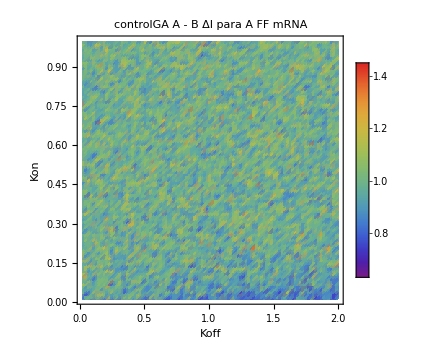
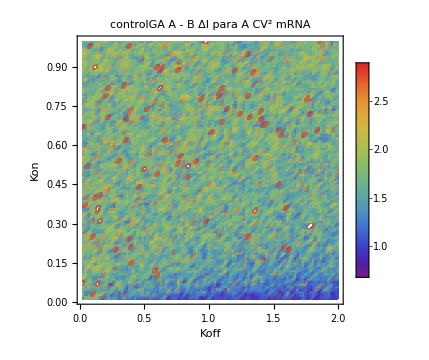
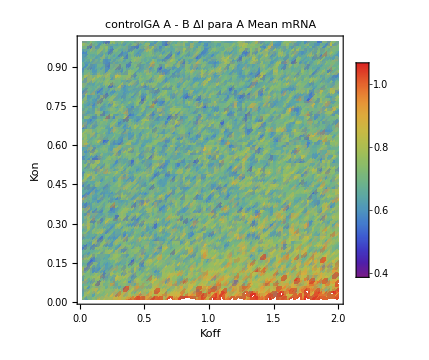
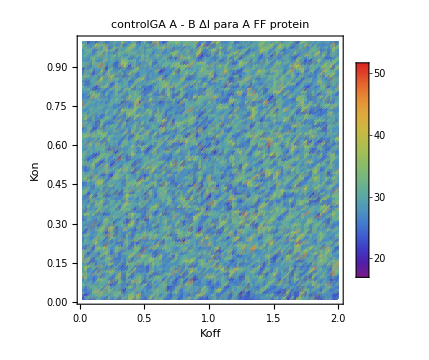
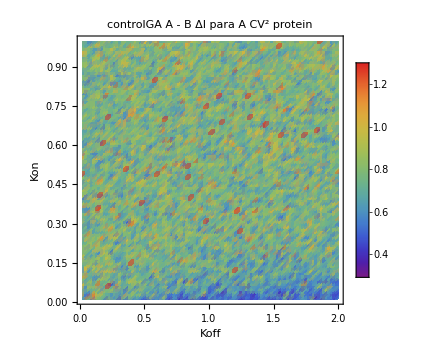
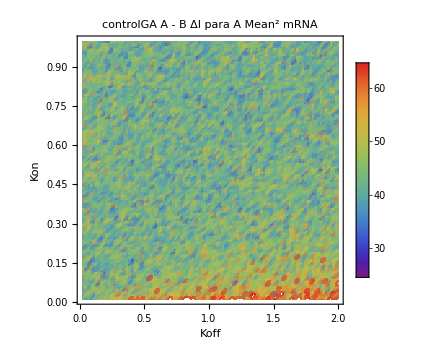

```mathematica
(****************************************************)Table[ListDensityPlot[i[[1]],PlotLabel->i[[2]],PlotLegends->Automatic,Frame-> True,FrameLabel->{"Koff","Kon"}(*{"Koff","Kon"}{"KdmRNA","Koff"}{"Kdp","KdmRNA"}*),DataRange->{{0.02,2},{0.01,1}(*{0.001,0.1},{0.01,1}{0.02,2}*)},ColorFunction->"Rainbow",ImageSize->Medium],{i,{{ffmRNA,ToString[modelo]<>" \n FF mRNA"},{cv2mRNA,ToString[modelo]<>" \n  CV^2 mRNA"},{meanmRNA,ToString[modelo]<>" \n  Mean mRNA"},{ffProtein,ToString[modelo]<>" \n  FF protein"},{cv2Protein,ToString[modelo]<>" \n  CV^2 protein"},{meanProtein,ToString[modelo]<>" \n  Mean^2 mRNA"}}}]
```

```mathematica
(***Para los que no cambian***)
```

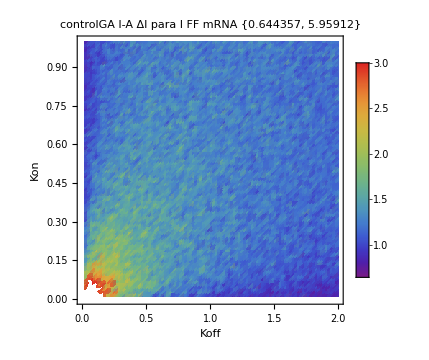
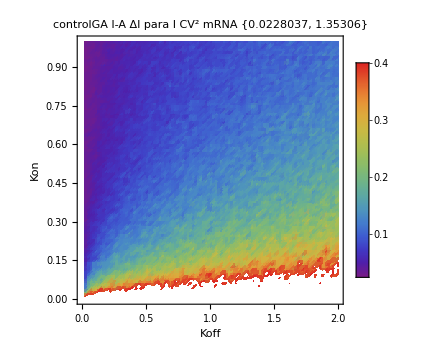
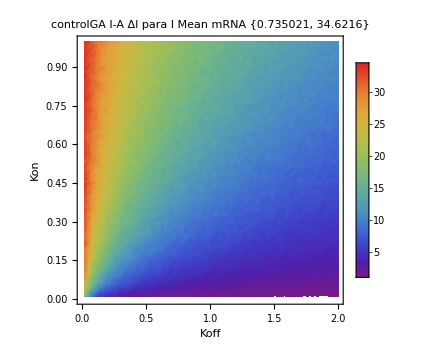
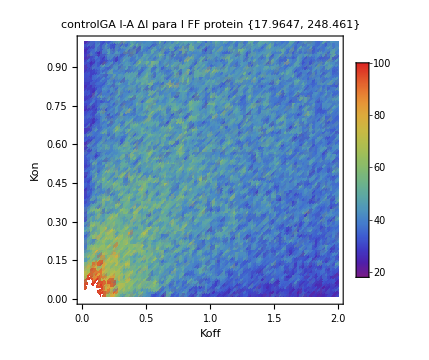
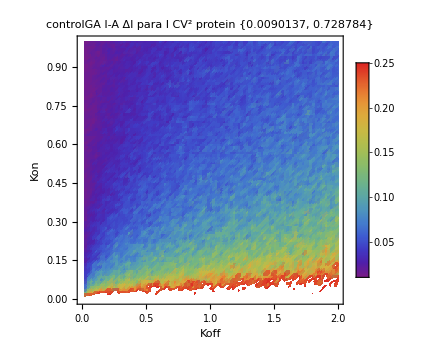
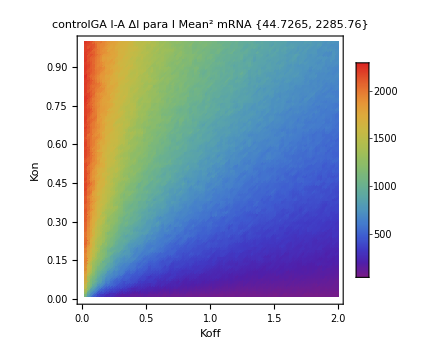

```mathematica
Table[ListDensityPlot[i[[1]],PlotLabel->i[[2]],PlotLegends->Automatic,Frame-> True,FrameLabel->{"Koff","Kon"}(*{"Koff","Kon"}{"KdmRNA","Koff"}{"Kdp","KdmRNA"}*),DataRange->{{0.02,2},{0.01,1}(*{0.001,0.1},{0.01,1}{0.02,2}*)},i[[3]],ColorFunction->"Rainbow",ImageSize->Medium],{i,{{ffmRNA,ToString[modelo]<>" \n FF mRNA "<>ToString[MinMax@Flatten@ffmRNA//N],PlotRange-> {0.45,3}},
{cv2mRNA,ToString[modelo]<>" \n  CV^2 mRNA "<>ToString[MinMax@Flatten@cv2mRNA//N],PlotRange->{0.02,0.4}},
{meanmRNA,ToString[modelo]<>" \n  Mean mRNA "<>ToString[MinMax@Flatten@meanmRNA//N],PlotRange->{1,35}},{ffProtein,ToString[modelo]<>" \n  FF protein "<>ToString[MinMax@Flatten@ffProtein//N],PlotRange-> {15,100}},{cv2Protein,ToString[modelo]<>" \n  CV^2 protein "<>ToString[MinMax@Flatten@cv2Protein//N],PlotRange->{0.01,0.25}},{meanProtein,ToString[modelo]<>" \n  Mean^2 mRNA "<>ToString[MinMax@Flatten@meanProtein//N],PlotRange->{50,2300}}}}]
```

```mathematica
ffmRNA[[1,1]]=0.45;ffmRNA[[1,2]]=3;
cv2mRNA[[1,1]]=0.6;cv2mRNA[[1,2]]=4;
meanmRNA[[1,1]]=0.3;meanmRNA[[1,2]]=1.2;
ffProtein[[1,1]]=15;ffProtein[[1,2]]=100;
cv2Protein[[1,1]]=0.3;cv2Protein[[1,2]]=1.65;
meanProtein[[1,1]]=10;meanProtein[[1,2]]=76;
```

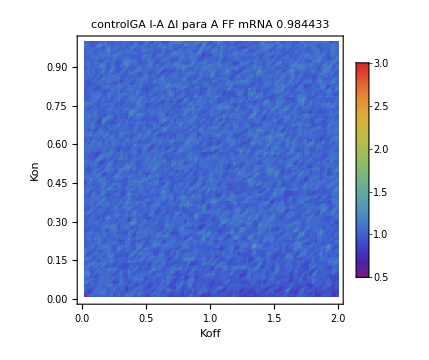
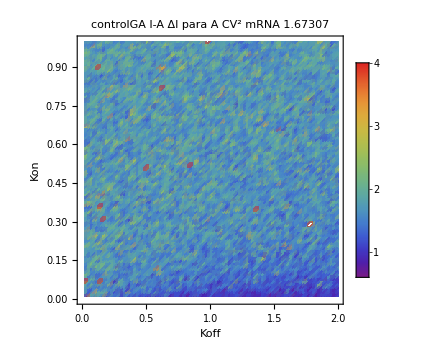
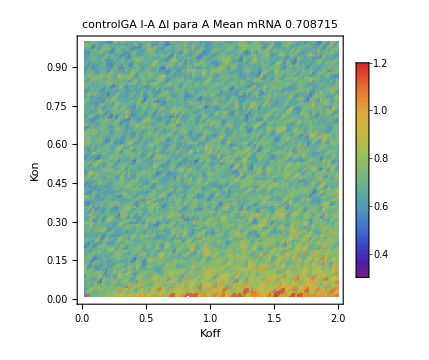
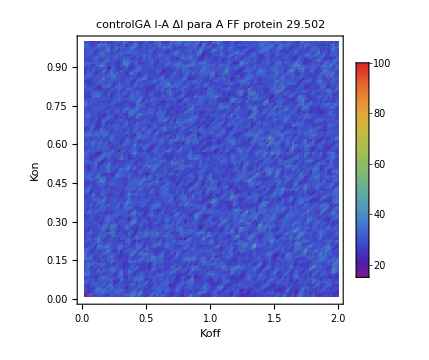
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ListDensityPlot[i[[1]],PlotLabel->i[[2]],PlotLegends->Automatic,Frame-> True,FrameLabel->{"Koff","Kon"}(*{"Koff","Kon"}{"KdmRNA","Koff"}{"Kdp","KdmRNA"}*),DataRange->{{0.02,2},{0.01,1}(*{0.001,0.1},{0.01,1}{0.02,2}*)},i[[3]],ColorFunction->"Rainbow",ImageSize->Medium],{i,{{ffmRNA,ToString[modelo]<>" \n FF mRNA "<>ToString[Mean@Flatten@ffmRNA//N],PlotRange-> {0.45,3}},
{cv2mRNA,ToString[modelo]<>" \n  CV^2 mRNA "<>ToString[Mean@Flatten@cv2mRNA//N],PlotRange->{0.6,4}},
{meanmRNA,ToString[modelo]<>" \n  Mean mRNA "<>ToString[Mean@Flatten@meanmRNA//N],PlotRange->{0.3,1.2}},{ffProtein,ToString[modelo]<>" \n  FF protein "<>ToString[Mean@Flatten@ffProtein//N],PlotRange-> {15,100}},{cv2Protein,ToString[modelo]<>" \n  CV^2 protein "<>ToString[Mean@Flatten@cv2Protein//N],PlotRange->{0.3,1.65}},{meanProtein,ToString[modelo]<>" \n  Mean^2 mRNA "<>ToString[Mean@Flatten@meanProtein//N],PlotRange->{10,76}}}}]
```

## Graphs for all systems in the same scale

### Importing-ordering data

```mathematica
(****NOTA IMPORTANTE!!!!!: Cuando tenga lista todos los de GA se hacen estas graficas con la misma escala para todas y poder comparar entre estas. Por el momento solo voy a revisar las que tengo*)
```

```mathematica
SetDirectory["/media/lina/DATA/SimulacionesTesis/resultadosS4/csv"];
```

```mathematica
(********************************kon-koff daata**)
data1=ToExpression@Table[Import["controlUnRGA_γg"<>i<>".csv"],{i,{"0.5","1.","1.5","2"}}];
data2=ToExpression@ImportString[#,"CSV"]&/@Table[Import["controlRGA_γg"<>i<>"2"],{i,{"0.5","1.","1.5.","2."}}];
data3=ToExpression@ImportString[#,"CSV"]&/@Table[Import["controlAIGAA_Aγg"<>i],{i,{"0.5","1.","1.5","2"}}];
data4=ToExpression@ImportString[#,"CSV"]&/@Table[Import["controlAIGAA_Iγg"<>i],{i,{"0.5","1.","1.5","2"}}];
data5=ToExpression@ImportString[#,"CSV"]&/@Table[Import["controlAIGAI_Aγg"<>i],{i,{"0.5","1.","1.5","2"}}];
data6=ToExpression@ImportString[#,"CSV"]&/@Table[Import["controlAIGAI_Iγg"<>i],{i,{"0.5","1.","1.5","2"}}];
```

```mathematica
(****************************************************)
```

```mathematica
data7=ToExpression@ImportString[#,"CSV"]&/@Table[Import["controlABGAA_AAγg"<>i],{i,{"0.5","1.","1.5","2"}}];(*cambiando A para A con el Activador*)
data8=ToExpression@ImportString[#,"CSV"]&/@Table[Import["controlABGAA_IAγg"<>i],{i,{"0.5","1.","1.5","2"}}];
(*cambiando A para I con el Activador*)
data7b=ToExpression@ImportString[#,"CSV"]&/@Table[Import["controlABGAI_AAγg"<>i],{i,{"0.5","1.","1.5","2"}}];(*cambiando I para A con el Activador*)
data8b=ToExpression@ImportString[#,"CSV"]&/@Table[Import["controlABGAI_IAγg"<>i],{i,{"0.5","1.","1.5","2"}}];
(*cambiando I para I con el Activador*)
```

```mathematica
(****************************************************)
```

```mathematica
data9=ToExpression@ImportString[#,"CSV"]&/@Table[Import["controlABGAA_AIγg"<>i],{i,{"0.5","1.","1.5","2"}}];
(*cambiando A para A con el Inhibidor*)
data10=ToExpression@ImportString[#,"CSV"]&/@Table[Import["controlABGAA_IIγg"<>i],{i,{"0.5","1.","1.5","2"}}];
(*cambiando A para I con el Inhibidor*)
data9b=ToExpression@ImportString[#,"CSV"]&/@Table[Import["controlABGAI_AIγg"<>i],{i,{"0.5","1.","1.5","2"}}];
(*cambiando I para A con el Inhibidor*)
data10b=ToExpression@ImportString[#,"CSV"]&/@Table[Import["controlABGAI_IIγg"<>i],{i,{"0.5","1.","1.5","2"}}];
(*cambiando I para I con el Inhibidor*)
```

```mathematica
(*******************************kmRNA-kp data)
```

```mathematica
data0=ToExpression@Table[Import["controlConstGA_γp"<>i,"CSV"],{i,{"0.025","0.05","0.075","0.1"}}];
```

```mathematica
data1=ToExpression@Table[Import["controlUnRGA_γp"<>i,"CSV"],{i,{"0.025","0.05","0.075","0.1"}}];
data2=ToExpression@Table[Import["controlRGA_γp"<>i,"CSV"],{i,{"0.025","0.05","0.075","0.1"}}];
data3=ToExpression@Table[Import["controlAIGAA_A_γp"<>i,"CSV"],{i,{"0.025","0.05","0.075","0.1"}}];
data4=ToExpression@Table[Import["controlAIGAA_I_γp"<>i,"CSV"],{i,{"0.025","0.05","0.075","0.1"}}];
data5=ToExpression@Table[Import["controlAIGAI_A_γp"<>i,"CSV"],{i,{"0.025","0.05","0.075","0.1"}}];
data6=ToExpression@Table[Import["controlAIGAI_I_γp"<>i,"CSV"],{i,{"0.025","0.05","0.075","0.1"}}];
```

```mathematica
(********************************************ordering data)
```

```mathematica
ffmRNA0=Map[Flatten,Transpose[Map[Partition[#,25]&,data0[[All,1(*mRNA*),All,1(*FF*)]]]]];
cv2mRNA0=Map[Flatten,Transpose[Map[Partition[#,25]&,data0[[All,1(*mRNA*),All,2(*cv2*)]]]]];
ffProtein0=Map[Flatten,Transpose[Map[Partition[#,25]&,data0[[All,2(*Protein*),All,1(*FF*)]]]]];
cv2Protein0=Map[Flatten,Transpose[Map[Partition[#,25]&,data0[[All,2(*Protein*),All,2(*cv2*)]]]]];
```

```mathematica
ffmRNA1=Map[Flatten,Transpose[Map[Partition[#,25]&,data1[[All,1(*mRNA*),All,1(*FF*)]]]]];
cv2mRNA1=Map[Flatten,Transpose[Map[Partition[#,25]&,data1[[All,1(*mRNA*),All,2(*cv2*)]]]]];
meanmRNA1=Map[Flatten,Transpose[Map[Partition[#,25]&,data1[[All,1(*mRNA*),All,3(*mean*)]]]]];
ffProtein1=Map[Flatten,Transpose[Map[Partition[#,25]&,data1[[All,2(*Protein*),All,1(*FF*)]]]]];
cv2Protein1=Map[Flatten,Transpose[Map[Partition[#,25]&,data1[[All,2(*Protein*),All,2(*cv2*)]]]]];
meanProtein1=Map[Flatten,Transpose[Map[Partition[#,25]&,data1[[All,2(*Protein*),All,3(*mean*)]]]]];
```

```mathematica
ffmRNA2=Map[Flatten,Transpose[Map[Partition[#,25]&,data2[[All,1(*mRNA*),All,1(*FF*)]]]]];
cv2mRNA2=Map[Flatten,Transpose[Map[Partition[#,25]&,data2[[All,1(*mRNA*),All,2(*cv2*)]]]]];
meanmRNA2=Map[Flatten,Transpose[Map[Partition[#,25]&,data2[[All,1(*mRNA*),All,3(*mean*)]]]]];
ffProtein2=Map[Flatten,Transpose[Map[Partition[#,25]&,data2[[All,2(*Protein*),All,1(*FF*)]]]]];
cv2Protein2=Map[Flatten,Transpose[Map[Partition[#,25]&,data2[[All,2(*Protein*),All,2(*cv2*)]]]]];
meanProtein2=Map[Flatten,Transpose[Map[Partition[#,25]&,data2[[All,2(*Protein*),All,3(*mean*)]]]]];
```

```mathematica
ffmRNA3=Map[Flatten,Transpose[Map[Partition[#,25]&,data3[[All,1(*mRNA*),All,1(*FF*)]]]]];
cv2mRNA3=Map[Flatten,Transpose[Map[Partition[#,25]&,data3[[All,1(*mRNA*),All,2(*cv2*)]]]]];
meanmRNA3=Map[Flatten,Transpose[Map[Partition[#,25]&,data3[[All,1(*mRNA*),All,3(*mean*)]]]]];
ffProtein3=Map[Flatten,Transpose[Map[Partition[#,25]&,data3[[All,2(*Protein*),All,1(*FF*)]]]]];
cv2Protein3=Map[Flatten,Transpose[Map[Partition[#,25]&,data3[[All,2(*Protein*),All,2(*cv2*)]]]]];
meanProtein3=Map[Flatten,Transpose[Map[Partition[#,25]&,data3[[All,2(*Protein*),All,3(*mean*)]]]]];
```

```mathematica
ffmRNA4=Map[Flatten,Transpose[Map[Partition[#,25]&,data4[[All,1(*mRNA*),All,1(*FF*)]]]]];
cv2mRNA4=Map[Flatten,Transpose[Map[Partition[#,25]&,data4[[All,1(*mRNA*),All,2(*cv2*)]]]]];
meanmRNA4=Map[Flatten,Transpose[Map[Partition[#,25]&,data4[[All,1(*mRNA*),All,3(*mean*)]]]]];
ffProtein4=Map[Flatten,Transpose[Map[Partition[#,25]&,data4[[All,2(*Protein*),All,1(*FF*)]]]]];
cv2Protein4=Map[Flatten,Transpose[Map[Partition[#,25]&,data4[[All,2(*Protein*),All,2(*cv2*)]]]]];
meanProtein4=Map[Flatten,Transpose[Map[Partition[#,25]&,data4[[All,2(*Protein*),All,3(*mean*)]]]]];
```

```mathematica
ffmRNA5=Map[Flatten,Transpose[Map[Partition[#,25]&,data5[[All,1(*mRNA*),All,1(*FF*)]]]]];
cv2mRNA5=Map[Flatten,Transpose[Map[Partition[#,25]&,data5[[All,1(*mRNA*),All,2(*cv2*)]]]]];
meanmRNA5=Map[Flatten,Transpose[Map[Partition[#,25]&,data5[[All,1(*mRNA*),All,3(*mean*)]]]]];
ffProtein5=Map[Flatten,Transpose[Map[Partition[#,25]&,data5[[All,2(*Protein*),All,1(*FF*)]]]]];
cv2Protein5=Map[Flatten,Transpose[Map[Partition[#,25]&,data5[[All,2(*Protein*),All,2(*cv2*)]]]]];
meanProtein5=Map[Flatten,Transpose[Map[Partition[#,25]&,data5[[All,2(*Protein*),All,3(*mean*)]]]]];
```

```mathematica
ffmRNA6=Map[Flatten,Transpose[Map[Partition[#,25]&,data6[[All,1(*mRNA*),All,1(*FF*)]]]]];
cv2mRNA6=Map[Flatten,Transpose[Map[Partition[#,25]&,data6[[All,1(*mRNA*),All,2(*cv2*)]]]]];
meanmRNA6=Map[Flatten,Transpose[Map[Partition[#,25]&,data6[[All,1(*mRNA*),All,3(*mean*)]]]]];
ffProtein6=Map[Flatten,Transpose[Map[Partition[#,25]&,data6[[All,2(*Protein*),All,1(*FF*)]]]]];
cv2Protein6=Map[Flatten,Transpose[Map[Partition[#,25]&,data6[[All,2(*Protein*),All,2(*cv2*)]]]]];
meanProtein6=Map[Flatten,Transpose[Map[Partition[#,25]&,data6[[All,2(*Protein*),All,3(*mean*)]]]]];
```

```mathematica
ffmRNA7=Map[Flatten,Transpose[Map[Partition[#,25]&,data7[[All,1(*mRNA*),All,1(*FF*)]]]]];
cv2mRNA7=Map[Flatten,Transpose[Map[Partition[#,25]&,data7[[All,1(*mRNA*),All,2(*cv2*)]]]]];
meanmRNA7=Map[Flatten,Transpose[Map[Partition[#,25]&,data7[[All,1(*mRNA*),All,3(*mean*)]]]]];
ffProtein7=Map[Flatten,Transpose[Map[Partition[#,25]&,data7[[All,2(*Protein*),All,1(*FF*)]]]]];
cv2Protein7=Map[Flatten,Transpose[Map[Partition[#,25]&,data7[[All,2(*Protein*),All,2(*cv2*)]]]]];
meanProtein7=Map[Flatten,Transpose[Map[Partition[#,25]&,data7[[All,2(*Protein*),All,3(*mean*)]]]]];
```

```mathematica
ffmRNA7b=Map[Flatten,Transpose[Map[Partition[#,25]&,data7b[[All,1(*mRNA*),All,1(*FF*)]]]]];
cv2mRNA7b=Map[Flatten,Transpose[Map[Partition[#,25]&,data7b[[All,1(*mRNA*),All,2(*cv2*)]]]]];
meanmRNA7b=Map[Flatten,Transpose[Map[Partition[#,25]&,data7b[[All,1(*mRNA*),All,3(*mean*)]]]]];
ffProtein7b=Map[Flatten,Transpose[Map[Partition[#,25]&,data7b[[All,2(*Protein*),All,1(*FF*)]]]]];
cv2Protein7b=Map[Flatten,Transpose[Map[Partition[#,25]&,data7b[[All,2(*Protein*),All,2(*cv2*)]]]]];
meanProtein7b=Map[Flatten,Transpose[Map[Partition[#,25]&,data7b[[All,2(*Protein*),All,3(*mean*)]]]]];
```

```mathematica
ffmRNA8=Map[Flatten,Transpose[Map[Partition[#,25]&,data8[[All,1(*mRNA*),All,1(*FF*)]]]]];
cv2mRNA8=Map[Flatten,Transpose[Map[Partition[#,25]&,data8[[All,1(*mRNA*),All,2(*cv2*)]]]]];
meanmRNA8=Map[Flatten,Transpose[Map[Partition[#,25]&,data8[[All,1(*mRNA*),All,3(*mean*)]]]]];
ffProtein8=Map[Flatten,Transpose[Map[Partition[#,25]&,data8[[All,2(*Protein*),All,1(*FF*)]]]]];
cv2Protein8=Map[Flatten,Transpose[Map[Partition[#,25]&,data8[[All,2(*Protein*),All,2(*cv2*)]]]]];
meanProtein8=Map[Flatten,Transpose[Map[Partition[#,25]&,data8[[All,2(*Protein*),All,3(*mean*)]]]]];
```

```mathematica
ffmRNA8b=Map[Flatten,Transpose[Map[Partition[#,25]&,data8b[[All,1(*mRNA*),All,1(*FF*)]]]]];
cv2mRNA8b=Map[Flatten,Transpose[Map[Partition[#,25]&,data8b[[All,1(*mRNA*),All,2(*cv2*)]]]]];
meanmRNA8b=Map[Flatten,Transpose[Map[Partition[#,25]&,data8b[[All,1(*mRNA*),All,3(*mean*)]]]]];
ffProtein8b=Map[Flatten,Transpose[Map[Partition[#,25]&,data8b[[All,2(*Protein*),All,1(*FF*)]]]]];
cv2Protein8b=Map[Flatten,Transpose[Map[Partition[#,25]&,data8b[[All,2(*Protein*),All,2(*cv2*)]]]]];
meanProtein8b=Map[Flatten,Transpose[Map[Partition[#,25]&,data8b[[All,2(*Protein*),All,3(*mean*)]]]]];
```

```mathematica
ffmRNA9=Map[Flatten,Transpose[Map[Partition[#,25]&,data9[[All,1(*mRNA*),All,1(*FF*)]]]]];
cv2mRNA9=Map[Flatten,Transpose[Map[Partition[#,25]&,data9[[All,1(*mRNA*),All,2(*cv2*)]]]]];
meanmRNA9=Map[Flatten,Transpose[Map[Partition[#,25]&,data9[[All,1(*mRNA*),All,3(*mean*)]]]]];
ffProtein9=Map[Flatten,Transpose[Map[Partition[#,25]&,data9[[All,2(*Protein*),All,1(*FF*)]]]]];
cv2Protein9=Map[Flatten,Transpose[Map[Partition[#,25]&,data9[[All,2(*Protein*),All,2(*cv2*)]]]]];
meanProtein9=Map[Flatten,Transpose[Map[Partition[#,25]&,data9[[All,2(*Protein*),All,3(*mean*)]]]]];
```

```mathematica
ffmRNA9b=Map[Flatten,Transpose[Map[Partition[#,25]&,data9b[[All,1(*mRNA*),All,1(*FF*)]]]]];
cv2mRNA9b=Map[Flatten,Transpose[Map[Partition[#,25]&,data9b[[All,1(*mRNA*),All,2(*cv2*)]]]]];
meanmRNA9b=Map[Flatten,Transpose[Map[Partition[#,25]&,data9b[[All,1(*mRNA*),All,3(*mean*)]]]]];
ffProtein9b=Map[Flatten,Transpose[Map[Partition[#,25]&,data9b[[All,2(*Protein*),All,1(*FF*)]]]]];
cv2Protein9b=Map[Flatten,Transpose[Map[Partition[#,25]&,data9b[[All,2(*Protein*),All,2(*cv2*)]]]]];
meanProtein9b=Map[Flatten,Transpose[Map[Partition[#,25]&,data9b[[All,2(*Protein*),All,3(*mean*)]]]]];
```

```mathematica
ffmRNA10=Map[Flatten,Transpose[Map[Partition[#,25]&,data10[[All,1(*mRNA*),All,1(*FF*)]]]]];
cv2mRNA10=Map[Flatten,Transpose[Map[Partition[#,25]&,data10[[All,1(*mRNA*),All,2(*cv2*)]]]]];
meanmRNA10=Map[Flatten,Transpose[Map[Partition[#,25]&,data10[[All,1(*mRNA*),All,3(*mean*)]]]]];
ffProtein10=Map[Flatten,Transpose[Map[Partition[#,25]&,data10[[All,2(*Protein*),All,1(*FF*)]]]]];
cv2Protein10=Map[Flatten,Transpose[Map[Partition[#,25]&,data10[[All,2(*Protein*),All,2(*cv2*)]]]]];
meanProtein10=Map[Flatten,Transpose[Map[Partition[#,25]&,data10[[All,2(*Protein*),All,3(*mean*)]]]]];
```

```mathematica
ffmRNA10b=Map[Flatten,Transpose[Map[Partition[#,25]&,data10b[[All,1(*mRNA*),All,1(*FF*)]]]]];
cv2mRNA10b=Map[Flatten,Transpose[Map[Partition[#,25]&,data10b[[All,1(*mRNA*),All,2(*cv2*)]]]]];
meanmRNA10b=Map[Flatten,Transpose[Map[Partition[#,25]&,data10b[[All,1(*mRNA*),All,3(*mean*)]]]]];
ffProtein10b=Map[Flatten,Transpose[Map[Partition[#,25]&,data10b[[All,2(*Protein*),All,1(*FF*)]]]]];
cv2Protein10b=Map[Flatten,Transpose[Map[Partition[#,25]&,data10b[[All,2(*Protein*),All,2(*cv2*)]]]]];
meanProtein10b=Map[Flatten,Transpose[Map[Partition[#,25]&,data10b[[All,2(*Protein*),All,3(*mean*)]]]]];
```